# Enhancing the SpokenString function output based on the input symbolic structure

Renan Germano

Mackenzie Presbyterian University

When dealing with graphs and images, the current SpokenString function returns a not significant text to the describe the input. The objective of the present project is to enhance this output by developing an algorithm that is capable of  better describing the input, based on its symbolic structure. Thinking about accessibility for visually impaired, this text could be used as an automatic generated alternative description for images and related contents.

## Wolfram Community Post (material for blog post)

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

## Complete project work

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

### Some Experiments

#### Named Colors

```mathematica
?WolframLanguageData
```

```mathematica
wlEntityProperties=WolframLanguageData["Properties"]
```

{attributes,character count,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,entity classes,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related guide pages,related symbols,relationship community graph,relationship graph,short notations,subject classifications,symbols linking to,symbols using as attribute,symbols using as option,text strings,timeline,timeline events,translations,typeset usage,URL,version introduced,version last modified,versions modified,Wolfram documentation link}

```mathematica
redNamedColorWLEntity=WolframLanguageData["Red"]
```

Red

```mathematica
entityPropertyValuesForRedColor={#,EntityValue[redNamedColorWLEntity, #]}&/@wlEntityProperties;
```

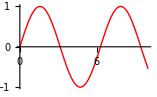
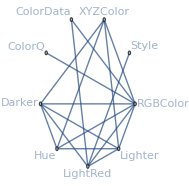
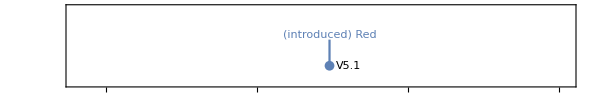
attributes | {Protected}
character count | 3
date introduced | Day: Mon 25 Oct 2004
documentation basic examples | {{Graphics[{Red,Disk[]}],-Graphics-,Plot[Sin[x],{x,0,10},PlotStyle→Red],-Graphics-,Graphics3D[{Red,Sphere[]}],-Graphics3D-}}
documentation example counts | {BasicExamples→1,Scope→0,GeneralizationsExtensions→0,Options→0,Applications→0,PropertiesRelations→0,PossibleIssues→0,InteractiveExamples→0,NeatExamples→0}
documentation example inputs | {BasicExamples→{{Graphics[{Red,Disk[]}],Plot[Sin[x],{x,0,10},PlotStyle→Red],Graphics3D[{Red,Sphere[]}]}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
documentation example text | {BasicExamples→{{}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
entity classes | {Wolfram Language autoevaluating symbols}
eponymous people | {}
external links | {}
frequencies of usage | {All→0.000434382,StackExchange→0.00233259,TypicalProductionCode→0.0010278,WolframAlphaCodebase→0.0000142108,WolframDemonstrations→0.00218411,WolframDocumentation→0.00162619}
full version introduced | 5.1
functionality areas | {ColorSymbols}
symbol background | Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style[hello,Red]).
Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].
Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.
link trails | {{guide/WolframRoot,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GraphicsOptionsAndStyling,guide/Colors,ref/Red},{guide/WolframRoot,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LifeSciencesAndMedicineDataAndComputation,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ProbabilityAndStatistics,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red}}
memberships | {Wolfram Language autoevaluating symbols}
name | Red
option names | {}
options | {}
plaintext usage | Red represents the color red in graphics or style specifications.
ranks of usage | {All→91,StackExchange→41,TypicalProductionCode→87,WolframAlphaCodebase→398,WolframDemonstrations→48,WolframDocumentation→54}
related entities | {red}
related guide pages | {Colorspaclet:guide/Colors,Symbolic Graphics Languagepaclet:guide/SymbolicGraphicsLanguage,Graphics Options & Stylingpaclet:guide/GraphicsOptionsAndStyling,Graphics Annotation & Appearancepaclet:guide/GraphicsAnnotationAndAppearance,Graphics Directivespaclet:guide/GraphicsDirectives,Maps & Cartographypaclet:guide/MapsAndCartography,Color Processingpaclet:guide/ColorProcessing,Notebook Formatting & Stylingpaclet:guide/NotebookFormattingAndStyling,Chart Styling & Layoutpaclet:guide/ChartLayoutAndStyling,Graph Visualizationpaclet:guide/GraphVisualization,Text Stylingpaclet:guide/TextStyling,GeoGraphics Languagepaclet:guide/GeoGraphicsLanguage,Graph Styling, Labeling, and Layoutpaclet:guide/GraphStylingAndLabeling,Maps & Cartographypaclet:guide/MapsAndGeographicData}
related symbols | {LightRed,ColorData,Lighter,Darker,Hue,RGBColor,Style}
relationship community graph | -Graphics-
relationship graph | -Graphics-
symbols linking to | {ColorQ,Hue,LightRed,RGBColor,XYZColor}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Red represents the color red in graphics or style specifications.,Red is equivalent to RGBColor[1,0,0].,Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style["hello",Red]).,Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].,Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.}
timeline | -Graphics-
timeline events | Day: Mon 25 Oct 2004Red
translations | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
typeset usage | Red represents the color red in graphics or style specifications. 
URL | http://reference.wolfram.com/language/ref/Red.html
version introduced | 5.1
Wolfram documentation link | Redpaclet:ref/Red

```mathematica
Grid[Select[entityPropertyValuesForRedColor, Not@MissingQ@Last@#&], Frame->All]
```

```mathematica
functionalityAreaOfAllWLSymbols={#, EntityValue[#,EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]}&/@wlSymbols;
```

```mathematica
colorSymbols=Select[functionalityAreaOfAllWLSymbols, (Length@Last@#)==1&&((First@Last@#)=="ColorSymbols")&]⟦All,1⟧
```

{Black,Blend,Blue,Brown,CMYKColor,ChromaticityPlot,ChromaticityPlot3D,ColorBalance,ColorCombine,ColorConvert,ColorCoverage,ColorData,ColorDataFunction,ColorDetect,ColorDistance,ColorFunction,ColorFunctionScaling,ColorNegate,ColorProfileData,ColorQ,ColorQuantize,ColorReplace,ColorRules,ColorSeparate,ColorSetter,ColorSpace,ColorToneMapping,Colorize,ColorsNear,Cyan,Darker,Dithering,FindMatchingColor,Glow,Gray,GrayLevel,Green,Hue,ImageColorSpace,LABColor,LCHColor,LUVColor,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Lighter,Magenta,MaxColorDistance,MinColorDistance,Orange,Pink,Purple,RGBColor,RandomColor,Red,StreamColorFunction,StreamColorFunctionScaling,VectorColorFunction,VectorColorFunctionScaling,White,WhitePoint,XYZColor,Yellow}

```mathematica
namedColors= Select[colorSymbols,ColorQ@RGBColor@#["Name"]&]
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightCyan,LightGreen,LightPink,LightYellow,Magenta,Orange,Pink,Purple,Red,White,Yellow}

```mathematica
Grid[{#, RGBColor@#@"Name", #@"Name", #@"Translations"}&/@namedColors, Frame->All]
```

Black | RGBColor[0., 0., 0.] | Black | {Simplified Chinese→黑色,Traditional Chinese→黑,French→noir,German→schwarz,Modern Greek→μαύρο,Japanese→黒,Korean→검정,Lithuanian→juodas,Polish→czarny,Portuguese→preto,Russian→чёрный,Spanish→negro,Ukrainian→чорний,Vietnamese→đen}
Blue | RGBColor[0., 0., 1.] | Blue | {Simplified Chinese→蓝色,Traditional Chinese→藍色,French→bleu,German→blau,Modern Greek→μπλε,Japanese→青,Korean→파랑,Lithuanian→mėlynas,Polish→niebieski,Portuguese→azul,Russian→синий,Spanish→azul,Ukrainian→синій,Vietnamese→xanh da trời}
Brown | RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412] | Brown | {Simplified Chinese→棕色,Traditional Chinese→棕色,French→marron,German→braun,Modern Greek→καφέ,Japanese→茶色,Korean→갈색,Lithuanian→rudas,Polish→brązowy,Portuguese→marrom,Russian→коричневый,Spanish→marrón,Ukrainian→коричневий,Vietnamese→nâu}
Cyan | RGBColor[0., 1., 1.] | Cyan | {Simplified Chinese→蓝绿色,Traditional Chinese→藍綠色,French→cyan,German→blaugrün,Modern Greek→κυανό,Japanese→シアン色,Korean→청록색,Lithuanian→žalsvai mėlynas,Polish→cyjan,Portuguese→azul turquesa,Russian→голубой,Spanish→cian,Ukrainian→блакитний,Vietnamese→lục lam}
Gray | RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | Gray | {Simplified Chinese→灰色,Traditional Chinese→灰,French→gris,German→grau,Modern Greek→γκρι,Japanese→灰色,Korean→회색,Lithuanian→pilkas,Polish→szary,Portuguese→cinza,Russian→серый,Spanish→gris,Ukrainian→сірий,Vietnamese→xám}
Green | RGBColor[0., 0.5019607843137255, 0.] | Green | {Simplified Chinese→绿色,Traditional Chinese→綠色,French→vert,German→grün,Modern Greek→πράσινο,Japanese→緑,Korean→녹색,Lithuanian→žalias,Polish→zielony,Portuguese→verde,Russian→зелёный,Spanish→verde,Ukrainian→зелений,Vietnamese→xanh lá}
LightBlue | RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726] | LightBlue | {Simplified Chinese→浅蓝色,Traditional Chinese→淡藍色,French→bleu clair,German→hellblau,Modern Greek→γαλάζιο,Japanese→水色,Korean→하늘색,Lithuanian→šviesiai mėlyna,Polish→jasnoniebieski,Portuguese→azul claro,Russian→светло-синий,Spanish→azul claro,Ukrainian→світло-синій,Vietnamese→xanh da trời nhạt}
LightCyan | RGBColor[0.87843137254902, 1., 1.] | LightCyan | {Simplified Chinese→淡青色,Traditional Chinese→淡青色,French→cyan clair,German→helles Blaugrün,Modern Greek→ανοιχτό κυανό,Japanese→薄いシアン色,Korean→밝은 청록색,Lithuanian→šviesiai žalsvai mėlyna,Polish→jasny cyjan,Portuguese→azul turquesa claro,Russian→светло-голубой,Spanish→cian claro,Ukrainian→світло-блакитний,Vietnamese→lục lam nhạt}
LightGreen | RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411] | LightGreen | {Simplified Chinese→浅绿,Traditional Chinese→淡綠色,French→vert clair,German→hellgrün,Modern Greek→ανοιχτό πράσινο,Japanese→薄緑色,Korean→연두색,Lithuanian→šviesiai žalia,Polish→jasnozielony,Portuguese→verde claro,Russian→светло-зелёный,Spanish→verde claro,Ukrainian→світло-зелений,Vietnamese→xanh lá cây nhạt}
LightPink | RGBColor[1., 0.7137254901960784, 0.7568627450980392] | LightPink | {Simplified Chinese→浅粉色,Traditional Chinese→淡粉色,French→rose clair,German→hellrosa,Modern Greek→ανοιχτό ροζ,Japanese→薄いピンク色,Korean→연분홍색,Lithuanian→šviesiai rausvos,Polish→jasnoróżowy,Portuguese→rosa claro,Russian→светло-розовый,Spanish→rosa claro,Ukrainian→світло-рожевий,Vietnamese→hồng nhạt}
LightYellow | RGBColor[1., 1., 0.87843137254902] | LightYellow | {Simplified Chinese→浅黄色,Traditional Chinese→淡黃色,French→jaune clair,German→hellgelb,Modern Greek→ανοιχτό κίτρινο,Japanese→薄い黄色,Korean→담황색,Lithuanian→šviesiai geltonos,Polish→jasnożółty,Portuguese→amarelo claro,Russian→светло-жёлтый,Spanish→amarillo claro,Ukrainian→світло-жовтий,Vietnamese→vàng nhạt}
Magenta | RGBColor[1., 0., 1.] | Magenta | {Simplified Chinese→品红色,Traditional Chinese→品紅色,French→magenta,German→magenta,Modern Greek→ματζέντα,Japanese→マジェンタ色,Korean→마젠타 색,Lithuanian→tamsiai raudonas,Polish→magenta,Portuguese→magenta,Russian→малиновый,Spanish→magenta,Ukrainian→малиновий,Vietnamese→đỏ tươi}
Orange | RGBColor[1., 0.6470588235294118, 0.] | Orange | {Simplified Chinese→橙色,Traditional Chinese→橙色,French→orange,German→orange,Modern Greek→πορτοκαλί,Japanese→オレンジ色,Korean→오렌지,Lithuanian→oranžinis,Polish→pomarańczowy,Portuguese→laranja,Russian→оранжевый,Spanish→naranja,Ukrainian→помаранчевий,Vietnamese→cam}
Pink | RGBColor[1., 0.7529411764705882, 0.796078431372549] | Pink | {Simplified Chinese→粉色,Traditional Chinese→粉紅色,French→rose,German→rosa,Modern Greek→ροζ,Japanese→ピンク色,Korean→분홍색,Lithuanian→rožinis,Polish→różowy,Portuguese→rosa,Russian→розовый,Spanish→rosa,Ukrainian→рожевий,Vietnamese→hồng}
Purple | RGBColor[0.5019607843137255, 0., 0.5019607843137255] | Purple | {Simplified Chinese→紫色,Traditional Chinese→紫色,French→violet,German→lila,Modern Greek→μωβ,Japanese→紫色,Korean→보라색,Lithuanian→purpurinis,Polish→purpurowy,Portuguese→roxo,Russian→фиолетовый,Spanish→púrpura,Ukrainian→фіолетовий,Vietnamese→tím}
Red | RGBColor[1., 0., 0.] | Red | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
White | RGBColor[1., 1., 1.] | White | {Simplified Chinese→白色,Traditional Chinese→白色,French→blanc,German→weiß,Modern Greek→λευκό,Japanese→白,Korean→흰색,Lithuanian→baltas,Polish→biały,Portuguese→branco,Russian→белый,Spanish→blanco,Ukrainian→білий,Vietnamese→trắng}
Yellow | RGBColor[1., 1., 0.] | Yellow | {Simplified Chinese→黄色,Traditional Chinese→黄色,French→jaune,German→gelb,Modern Greek→κίτρινο,Japanese→黄色,Korean→노란색,Lithuanian→geltonas,Polish→żółty,Portuguese→amarelo,Russian→жёлтый,Spanish→amarillo,Ukrainian→жовтий,Vietnamese→vàng}

```mathematica
namedColorsRGB=Association[RGBColor@#@"Name"->#&/@namedColors]
```

<|RGBColor[0., 0., 0.]→Black,RGBColor[0., 0., 1.]→Blue,RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]→Brown,RGBColor[0., 1., 1.]→Cyan,RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]→Gray,RGBColor[0., 0.5019607843137255, 0.]→Green,RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]→LightBlue,RGBColor[0.87843137254902, 1., 1.]→LightCyan,RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]→LightGreen,RGBColor[1., 0.7137254901960784, 0.7568627450980392]→LightPink,RGBColor[1., 1., 0.87843137254902]→LightYellow,RGBColor[1., 0., 1.]→Magenta,RGBColor[1., 0.6470588235294118, 0.]→Orange,RGBColor[1., 0.7529411764705882, 0.796078431372549]→Pink,RGBColor[0.5019607843137255, 0., 0.5019607843137255]→Purple,RGBColor[1., 0., 0.]→Red,RGBColor[1., 1., 1.]→White,RGBColor[1., 1., 0.]→Yellow|>

```mathematica
MyColorDistance[color1_RGBColor,color2_RGBColor]:=N[Mean[MapThread[Abs[#1-#2]&,{List@@color1,List@@color2}]]]
MyColorDistance[Red,Red]
MyColorDistance[Red,Green]
MyColorDistance[Red,Blue]
MyColorDistance[Red,Pink]
MyColorDistance[Red,Black]
```

0.

0.666667

0.666667

0.333333

MyColorDistance[RGBColor[1, 0, 0],GrayLevel[0]]

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
nearestColor = Nearest[Keys@namedColorsRGB,randomColor,1]//First
namedColorsRGB[nearestColor]["Name"]
Association[namedColorsRGB[nearestColor]["Translations"]][Entity["Language","Portuguese"]]
```

RGBColor[0.4891613857651431, 0.7106883893395335, 0.8812434631419106]

RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]

LightBlue

azul claro

```mathematica
Clear[Description]
```

```mathematica
Description[color_RGBColor]:=Description[color]=namedColorsRGB[First@Nearest[Keys@namedColorsRGB,color,1]]@"Name"
```

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description[randomColor]
```

RGBColor[0.6487446020354917, 0.8828059023758048, 0.019641943046032617]

Yellow

```mathematica
tests={#, Style[Description@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[tests,{5,20,2}]
```

{RGBColor[{0.7957698526502079, 0.12859848697380527, 0.06200807597333746}] | Red
RGBColor[{0.8904931699804928, 0.7232962892764894, 0.1986682303577123}] | Orange
RGBColor[{0.17933681495241638, 0.7071500810527913, 0.5419821935038365}] | LightGreen
RGBColor[{0.04131190638906612, 0.0248780352331035, 0.36634176681462827}] | Purple
RGBColor[{0.04175396491914163, 0.5007155330126138, 0.16137770214748848}] | Green
RGBColor[{0.9097077589101223, 0.3349650812809153, 0.04593459850536474}] | Red
RGBColor[{0.06293154302760806, 0.6511312610185693, 0.7586347460668852}] | LightBlue
RGBColor[{0.9684173967249148, 0.7936285477627292, 0.09769280045939577}] | Orange
RGBColor[{0.12815022764693418, 0.666170083577494, 0.5805273065617027}] | Cyan
RGBColor[{0.7597013509717332, 0.6857697954184974, 0.49658292492260414}] | LightYellow
RGBColor[{0.009899882153530104, 0.9430030494134345, 0.26478903099549855}] | LightGreen
RGBColor[{0.8336729384210131, 0.2172994776791639, 0.10751528642292807}] | Brown
RGBColor[{0.8555523678645336, 0.8530892806454957, 0.04535297877004307}] | Yellow
RGBColor[{0.32715884059692923, 0.25748271560007674, 0.6458990431929628}] | Purple
RGBColor[{0.2440833000115683, 0.06784377043239753, 0.48234619912701593}] | Purple
RGBColor[{0.5303380038984626, 0.4441041616833037, 0.3730584113540105}] | Gray
RGBColor[{0.0692850120544819, 0.6857357693452342, 0.07405609494327448}] | Green
RGBColor[{0.5940235557312568, 0.4840351999918624, 0.5750956946474093}] | Gray
RGBColor[{0.24091783286805057, 0.17429362876067556, 0.6133973201339182}] | Purple
RGBColor[{0.9556377240164844, 0.8503100592902075, 0.24856698288136592}] | Yellow,RGBColor[{0.6850035753874182, 0.5343925796625761, 0.3223101014750014}] | Gray
RGBColor[{0.5545249227416296, 0.38165027339794344, 0.013981319110859092}] | Brown
RGBColor[{0.633713862967552, 0.380815750791067, 0.2598727053155865}] | Brown
RGBColor[{0.3835796361026207, 0.26332622326808663, 0.19117595534579568}] | Gray
RGBColor[{0.04418561125279519, 0.6689619987698776, 0.8015652271713662}] | LightBlue
RGBColor[{0.5315790879727953, 0.33628811907688916, 0.492278757281021}] | Gray
RGBColor[{0.3261863310895343, 0.6589569799517201, 0.21395096189663887}] | Green
RGBColor[{0.8571705537096836, 0.03993021400612262, 0.6679326181490579}] | Purple
RGBColor[{0.347734569658245, 0.1634141842658683, 0.5559756721967237}] | Purple
RGBColor[{0.769147820891489, 0.650244569731727, 0.47426240382295837}] | Pink
RGBColor[{0.6710852055855401, 0.6107137052740539, 0.77910293232007}] | Gray
RGBColor[{0.0707255312132109, 0.6773271330074355, 0.7848665416179468}] | LightBlue
RGBColor[{0.620067445690849, 0.7600601115313217, 0.46268012298286076}] | LightGreen
RGBColor[{0.776540702934716, 0.5617478876190916, 0.14274428804583406}] | Orange
RGBColor[{0.47181034516388154, 0.17983287124890546, 0.1956479474582704}] | Brown
RGBColor[{0.9491550474113584, 0.7277106220796865, 0.021996827279103792}] | Orange
RGBColor[{0.4742620157046793, 0.5988480465711714, 0.010450015359265707}] | Green
RGBColor[{0.8700749702009862, 0.7675163684876014, 0.2404618409570447}] | Orange
RGBColor[{0.1615076132205393, 0.27377696127491613, 0.17964595328523236}] | Gray
RGBColor[{0.7403380339611063, 0.5536075823807542, 0.14946668428950205}] | Orange,RGBColor[{0.03937061093696359, 0.7608539291941925, 0.9582975101379885}] | LightBlue
RGBColor[{0.9134761266630917, 0.63312496793405, 0.7759312190502212}] | LightPink
RGBColor[{0.5780395785630668, 0.31193329763516253, 0.3436394465222763}] | Brown
RGBColor[{0.8008378755471217, 0.08141032674699233, 0.613378795966012}] | Purple
RGBColor[{0.1849075831029552, 0.5544559713790356, 0.03246138085180439}] | Green
RGBColor[{0.8112645098704816, 0.053886163485505456, 0.5855687430962335}] | Purple
RGBColor[{0.48336441122769935, 0.7615732181964558, 0.5480521718462859}] | LightGreen
RGBColor[{0.8687445179817772, 0.0034383446172816523, 0.13134545779340812}] | Red
RGBColor[{0.9203430347220822, 0.06803689955106806, 0.11914877504548493}] | Red
RGBColor[{0.07337680543570535, 0.6402273877317388, 0.6302546433944429}] | LightBlue
RGBColor[{0.09960314799280345, 0.7325218527312927, 0.9654282307502611}] | LightBlue
RGBColor[{0.5863020284933935, 0.12117777068005275, 0.6242850320209548}] | Purple
RGBColor[{0.2751994841543661, 0.29370452180454265, 0.7696152476117124}] | Purple
RGBColor[{0.48841807669353376, 0.3916555859712496, 0.694698992387955}] | Purple
RGBColor[{0.2692974614448804, 0.7143138179799697, 0.5305588656166305}] | LightGreen
RGBColor[{0.9636135845933564, 0.8689496450967931, 0.5555164433546222}] | LightYellow
RGBColor[{0.6698505603508873, 0.6780468939261559, 0.9767192420915096}] | LightBlue
RGBColor[{0.1182056946561385, 0.8383259883155485, 0.2751268711828381}] | LightGreen
RGBColor[{0.3045708654074124, 0.23095705635342645, 0.7580625930390541}] | Purple
RGBColor[{0.27312106533824876, 0.7991818823980736, 0.8379306960775776}] | Cyan,RGBColor[{0.8937257715519704, 0.8807536911720057, 0.9817172285500875}] | White
RGBColor[{0.15320832383331173, 0.512296457862405, 0.9059993053487292}] | LightBlue
RGBColor[{0.6657809263530785, 0.33889885967720357, 0.8021437785072543}] | Purple
RGBColor[{0.9310191606759082, 0.9846765336359895, 0.22895133426834335}] | Yellow
RGBColor[{0.3258499182048875, 0.6079761346607218, 0.656812047542531}] | LightBlue
RGBColor[{0.4018164531303643, 0.7917401769490047, 0.9903745767935361}] | LightBlue
RGBColor[{0.8502782179353137, 0.46578227914301706, 0.865928478336649}] | Purple
RGBColor[{0.9615618533991928, 0.14382501350976606, 0.0540799289838787}] | Red
RGBColor[{0.0023392020559258597, 0.38467988831580935, 0.020063242925447478}] | Green
RGBColor[{0.904622210063619, 0.07867347259062063, 0.4162900811262258}] | Brown
RGBColor[{0.14134397600044912, 0.1144101392759016, 0.16593146932077896}] | Black
RGBColor[{0.8297660810096466, 0.8616187455806332, 0.47844272387192976}] | LightGreen
RGBColor[{0.5061936112837391, 0.7486405467660333, 0.006455944623415588}] | Green
RGBColor[{0.587292561097708, 0.9640731895619195, 0.8250348263769987}] | Cyan
RGBColor[{0.7662770525232347, 0.9047614656553804, 0.5911087103888437}] | LightGreen
RGBColor[{0.9717726789346031, 0.15440132325057676, 0.6168329618147808}] | Purple
RGBColor[{0.2501927973861149, 0.5978712027841842, 0.2412484363921592}] | Green
RGBColor[{0.23470713940096188, 0.6767583408709359, 0.9742148569176587}] | LightBlue
RGBColor[{0.2143414854334209, 0.6345131308939653, 0.6135471491694215}] | LightBlue
RGBColor[{0.41072428286276996, 0.459486804833221, 0.5131606918971965}] | Gray,RGBColor[{0.7787080424515205, 0.44533408841291666, 0.7102868122558921}] | Purple
RGBColor[{0.6024740114957285, 0.18656882267687847, 0.7422666112046321}] | Purple
RGBColor[{0.27128650829840906, 0.008765641509560052, 0.6421065209765586}] | Purple
RGBColor[{0.9049287367387102, 0.7315326830346207, 0.6269153114279613}] | Pink
RGBColor[{0.029334617633246518, 0.8819209781200339, 0.6063705595116236}] | LightGreen
RGBColor[{0.048222930650910545, 0.7795096084538007, 0.7225590542134628}] | Cyan
RGBColor[{0.9387530959932797, 0.6720954099401049, 0.049072562273820175}] | Orange
RGBColor[{0.4797108323429182, 0.5794335687565761, 0.0085038796622241}] | Green
RGBColor[{0.8796644153256523, 0.3373249233568363, 0.28890900065717706}] | Brown
RGBColor[{0.6821237375187912, 0.3810579839400947, 0.6787081596938749}] | Purple
RGBColor[{0.8667785669829753, 0.4477181105691661, 0.22922896392422776}] | Brown
RGBColor[{0.4410687255161285, 0.43445321931801684, 0.5388348317416007}] | Gray
RGBColor[{0.9825356912156336, 0.5458157035191369, 0.7210789997178184}] | LightPink
RGBColor[{0.38964697050062136, 0.7645531436052175, 0.1601066394344548}] | Green
RGBColor[{0.982659457347137, 0.3859973607043823, 0.36161178055856436}] | Brown
RGBColor[{0.16064384883162108, 0.3661786930966111, 0.7457019939429306}] | Purple
RGBColor[{0.5536272706589893, 0.811713855054855, 0.8666550348472535}] | LightBlue
RGBColor[{0.675446319407023, 0.8022115601469881, 0.24066004119241424}] | LightGreen
RGBColor[{0.07500040022265031, 0.8428544807092961, 0.8807016539595747}] | Cyan
RGBColor[{0.5929438244783265, 0.28906107570785466, 0.11005441350281142}] | Brown}

```mathematica
$Language
```

English

```mathematica
Clear[TranslatedDescription]
```

```mathematica
TranslatedDescription[color_RGBColor]:=TranslatedDescription[color]=Description[color]
TranslatedDescription[color_RGBColor,language_String]:=TranslatedDescription[color,language]=Association[namedColorsRGB[First@Nearest[Keys@namedColorsRGB,color,1]]["Translations"]][Entity["Language",language]]
```

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
TranslatedDescription[randomColor,"Japanese"]
```

RGBColor[0.6359801969383037, 0.2983988016449226, 0.1881533837740761]

茶色

```mathematica
tests2={#, Style[Description@#,#],Style[TranslatedDescription[#,"Spanish"],#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[tests2,{5,20,3}]
```

{RGBColor[{0.6079445684942844, 0.38885980621737515, 0.25836645001689407}] | Brown | marrón
RGBColor[{0.06036433845011069, 0.7884228905729023, 0.04983416858918677}] | Green | verde
RGBColor[{0.5209272885582648, 0.26500642882992986, 0.7882785930047183}] | Purple | púrpura
RGBColor[{0.25498514243051185, 0.21215072030524396, 0.2274112208861363}] | Black | negro
RGBColor[{0.40144622679142183, 0.3193509178844436, 0.5542221361827264}] | Purple | púrpura
RGBColor[{0.41389832760772993, 0.09444835939067797, 0.6555875286904251}] | Purple | púrpura
RGBColor[{0.3912831953431948, 0.5968392468672918, 0.7648531150954214}] | LightBlue | azul claro
RGBColor[{0.23653780849860073, 0.012169410953481119, 0.6965900089448569}] | Blue | azul
RGBColor[{0.9813362424079881, 0.17890553766711048, 0.31838395995877455}] | Brown | marrón
RGBColor[{0.7660459235401023, 0.06216143670831831, 0.6671298971066801}] | Purple | púrpura
RGBColor[{0.5430177990121916, 0.6867403102346652, 0.8613768119294669}] | LightBlue | azul claro
RGBColor[{0.11703999730140002, 0.7170218955092309, 0.3031998726406928}] | Green | verde
RGBColor[{0.47645973042252576, 0.8356959108554203, 0.9062142914679183}] | LightBlue | azul claro
RGBColor[{0.8225880277829418, 0.9038064389798073, 0.9833054386109159}] | LightBlue | azul claro
RGBColor[{0.8307861171652113, 0.5597588612802611, 0.8254825698359101}] | LightPink | rosa claro
RGBColor[{0.2113662934206233, 0.20437220288751923, 0.08305368347157205}] | Black | negro
RGBColor[{0.7053942871147898, 0.24772678523317326, 0.6169020366390958}] | Purple | púrpura
RGBColor[{0.08663150688832855, 0.5471835951191453, 0.26248624881861815}] | Green | verde
RGBColor[{0.9460600619848933, 0.9309050714716953, 0.9523794408795303}] | White | blanco
RGBColor[{0.8389012191483634, 0.7831951915556388, 0.963823119024726}] | LightBlue | azul claro,RGBColor[{0.9984781175845752, 0.38869477018735776, 0.817644381366565}] | Purple | púrpura
RGBColor[{0.48584488316021, 0.38238052233094466, 0.5923398809891691}] | Gray | gris
RGBColor[{0.1654284061449074, 0.6223415977033249, 0.7943793381168709}] | LightBlue | azul claro
RGBColor[{0.04628708299257456, 0.7102370030093399, 0.8867159573919194}] | LightBlue | azul claro
RGBColor[{0.3200408403533992, 0.0458032827954542, 0.6642407909893715}] | Purple | púrpura
RGBColor[{0.9222295206709115, 0.46414189803720607, 0.026532013452637004}] | Orange | naranja
RGBColor[{0.987838104449809, 0.8714348134066496, 0.44734027012266275}] | Orange | naranja
RGBColor[{0.16642731110013487, 0.6437583723511076, 0.3619947338533056}] | Green | verde
RGBColor[{0.9966922556254911, 0.6256146609318636, 0.9049202499164692}] | LightPink | rosa claro
RGBColor[{0.7251607501511366, 0.23144645987796997, 0.2849950376023682}] | Brown | marrón
RGBColor[{0.07163997699393687, 0.09892575440549134, 0.513012460732424}] | Purple | púrpura
RGBColor[{0.744009093146045, 0.059354710325694615, 0.5978559257921416}] | Purple | púrpura
RGBColor[{0.3205658849707449, 0.6400945701682526, 0.36377152678448454}] | Green | verde
RGBColor[{0.42803123111634456, 0.5988682710369715, 0.8008870898719302}] | LightBlue | azul claro
RGBColor[{0.6247802035083578, 0.8888518423272231, 0.20502875061996395}] | LightGreen | verde claro
RGBColor[{0.8731258006129041, 0.15596247826774, 0.20595124266496279}] | Brown | marrón
RGBColor[{0.6029893836635989, 0.9594556662848948, 0.043310916361231744}] | Yellow | amarillo
RGBColor[{0.44126270173558213, 0.9643937149754156, 0.2125921844655645}] | LightGreen | verde claro
RGBColor[{0.012145592945770112, 0.299614166501331, 0.9098799610495836}] | Blue | azul
RGBColor[{0.4515839908878232, 0.02468606574287091, 0.7917654275406776}] | Blue | azul,RGBColor[{0.8468076709165813, 0.6193214972444707, 0.6730442042798819}] | LightPink | rosa claro
RGBColor[{0.2354972137131348, 0.6944295015438109, 0.5726706955995275}] | Cyan | cian
RGBColor[{0.45232391847512443, 0.3865938305671943, 0.6891322855271731}] | Purple | púrpura
RGBColor[{0.3744225331018387, 0.5564083230954333, 0.8893671521364568}] | LightBlue | azul claro
RGBColor[{0.048541035763824514, 0.4905283460181604, 0.7915696854041063}] | Gray | gris
RGBColor[{0.6229363384378184, 0.202446860724945, 0.3594682689756816}] | Brown | marrón
RGBColor[{0.747186691962274, 0.16305168078117416, 0.5753925081693818}] | Purple | púrpura
RGBColor[{0.9912903101519179, 0.028275375854120766, 0.6459696287615349}] | Purple | púrpura
RGBColor[{0.38440098192332894, 0.669096884704421, 0.16791076327866206}] | Green | verde
RGBColor[{0.931842132661252, 0.3217459217563903, 0.27188785498395474}] | Brown | marrón
RGBColor[{0.11345142019305876, 0.05047882302216822, 0.3285474341272079}] | Purple | púrpura
RGBColor[{0.873853031903558, 0.24012501535757425, 0.7387733117978346}] | Purple | púrpura
RGBColor[{0.5003143673148003, 0.9951548546516211, 0.47922244177436824}] | LightGreen | verde claro
RGBColor[{0.4662217252151397, 0.03240195153539349, 0.17482965110680992}] | Brown | marrón
RGBColor[{0.5955756394949974, 0.981952379914993, 0.3262831804404176}] | LightGreen | verde claro
RGBColor[{0.4569115403150037, 0.3620976308863393, 0.769498574490977}] | Purple | púrpura
RGBColor[{0.7703646629095182, 0.42645066385636565, 0.44980877385374973}] | LightPink | rosa claro
RGBColor[{0.8146423687952089, 0.8983873946717738, 0.3918927079900363}] | LightGreen | verde claro
RGBColor[{0.5733565878448226, 0.7504890570119511, 0.6021211810566065}] | LightBlue | azul claro
RGBColor[{0.09696499035010597, 0.02642075300341773, 0.9128763800402149}] | Blue | azul,RGBColor[{0.3809038604957613, 0.795100917445446, 0.5075074642838953}] | LightGreen | verde claro
RGBColor[{0.7650423399511224, 0.9904901782048194, 0.7241219515594932}] | LightGreen | verde claro
RGBColor[{0.0005163783116595155, 0.9121946114247117, 0.5300502420270952}] | LightGreen | verde claro
RGBColor[{0.3627308612075113, 0.6690775834138796, 0.24875831494573442}] | Green | verde
RGBColor[{0.4406413283713555, 0.8768508451983241, 0.9608270223013831}] | LightBlue | azul claro
RGBColor[{0.8583343935283401, 0.941590663411298, 0.7697398275912852}] | LightYellow | amarillo claro
RGBColor[{0.5849498679626759, 0.49986960840369843, 0.8143887705154693}] | Purple | púrpura
RGBColor[{0.6512437842013166, 0.7785229019529838, 0.46915448032210594}] | LightGreen | verde claro
RGBColor[{0.648494851271495, 0.23091797552966442, 0.9123122719592929}] | Magenta | magenta
RGBColor[{0.29752106084599816, 0.605051773562546, 0.6122798110584602}] | Gray | gris
RGBColor[{0.22129262939019712, 0.17847460768287315, 0.1416555157244357}] | Black | negro
RGBColor[{0.6102697838629596, 0.7995591759326157, 0.7021866178129919}] | LightBlue | azul claro
RGBColor[{0.000029414514067793718, 0.17185192355931833, 0.40481717606361456}] | Black | negro
RGBColor[{0.9442165668786258, 0.144551247136399, 0.4439446996606575}] | Brown | marrón
RGBColor[{0.20054201400786087, 0.018451345970927235, 0.1912570599664849}] | Black | negro
RGBColor[{0.4675606417104554, 0.6217608363082352, 0.5674047900347683}] | Gray | gris
RGBColor[{0.7503123688229383, 0.9034874433578133, 0.05367908987815939}] | Yellow | amarillo
RGBColor[{0.21314415191756098, 0.5728362649071592, 0.21580152444727374}] | Green | verde
RGBColor[{0.7013003850185671, 0.23044966207713458, 0.9010624198443162}] | Magenta | magenta
RGBColor[{0.39305867106474257, 0.9763083047432848, 0.729925098220773}] | LightGreen | verde claro,RGBColor[{0.5915639806014183, 0.9849288513583521, 0.8418409897948111}] | Cyan | cian
RGBColor[{0.0859767716189821, 0.5302356694112267, 0.5946761548406614}] | Gray | gris
RGBColor[{0.48527620846452724, 0.6444866289575202, 0.41976877356691356}] | LightGreen | verde claro
RGBColor[{0.40094048331766197, 0.5207568135611635, 0.6817899422277351}] | Gray | gris
RGBColor[{0.597634104587661, 0.5701524286489477, 0.5225674901121464}] | Gray | gris
RGBColor[{0.6202009719620816, 0.5549452535686688, 0.3057725272172096}] | Gray | gris
RGBColor[{0.2321902769707178, 0.9364714315221203, 0.22223211819669642}] | LightGreen | verde claro
RGBColor[{0.2153018347270803, 0.12144249502115789, 0.7564259641509996}] | Blue | azul
RGBColor[{0.9762929618730676, 0.4268069353107804, 0.058774276425024086}] | Orange | naranja
RGBColor[{0.8864803141414177, 0.6948984589655696, 0.6334898441135239}] | Pink | rosa
RGBColor[{0.658918110528983, 0.7375832478453517, 0.8600812189086087}] | LightBlue | azul claro
RGBColor[{0.3143218140903492, 0.1965463641758165, 0.660230195767038}] | Purple | púrpura
RGBColor[{0.26198112961617737, 0.2106451898955839, 0.6832057637639883}] | Purple | púrpura
RGBColor[{0.9782003318067503, 0.32020756532782757, 0.3877133507624755}] | Brown | marrón
RGBColor[{0.7330041755431143, 0.6731972954684129, 0.5468129165963007}] | Gray | gris
RGBColor[{0.7375346305149046, 0.9186136627275066, 0.9007819105592862}] | LightCyan | cian claro
RGBColor[{0.3578063601018966, 0.053190939223861644, 0.8313165742117996}] | Blue | azul
RGBColor[{0.44673566659058395, 0.5869526569390029, 0.6770939659510853}] | Gray | gris
RGBColor[{0.7153316496503526, 0.23519787285050575, 0.5247932457896294}] | Purple | púrpura
RGBColor[{0.027464627630154892, 0.6252997318189524, 0.965860617789992}] | LightBlue | azul claro}

#### ColorDat

```mathematica
colors=Select[Flatten[ColorData[#,"ColorList"]&/@Flatten[ColorData/@ColorData[]]],!MissingQ[#]&]//Join//Sort;
```

```mathematica
colors//Length
colors[[;;10]]
```

2143

{GrayLevel[0.393668],GrayLevel[0.501961],GrayLevel[0.642527],GrayLevel[0.660639],GrayLevel[1],Hue[0, 0.33, 0.6],Hue[0, 0.33, 0.66],Hue[0, 0.5, 0.44],Hue[0, 0.5, 0.6],Hue[0, 0.5, 0.85]}

#### Entity Color

```mathematica
allColorEntities = EntityValue["Color", "Entities"];
```

```mathematica
allColorEntities//Length
```

10386

```mathematica
EntityValue["Color", "Properties"]
```

{analogous colors,brightness,CIE  L^*a^*b^*,CMYK,color split-complements,color tetrad,color triad,complementary color,complementary colors,entity classes,gray level,hexadecimal,HSB,HSI,HSL,HSV,hue,Hunter  Lab,intensity,lightness,L^*u^*v^*,monochromatic colors,name,flags with nearby colors,flags with nearby colors,nearest named brand colors,nearest named HTML colors,nearest Pantone colors,24-bit RGB,saturation,24-bit sRGB,Wolfram Language,xyY,XYZ}

```mathematica
nameAndColorEntities=EntityValue[EntityValue["Color", "Entities"],{EntityProperty["Color","Name"],EntityProperty["Color","RGBValue"]}]
```

{{HTML peach,color red:1. green:0.854902 blue:0.72549},{Colorado Yellow,color red:0.956863 green:0.858824 blue:0.517647},{Condor Yellow,color red:0.929412 green:0.92549 blue:0.654902},{Sahara,color red:0.929412 green:0.827451 blue:0.654902},{Ceylon Gold Metallic,color red:0.862745 green:0.752941 blue:0.454902},{Sienna Brown Metallic,color red:0.376471 green:0.196078 blue:0.137255},{Sierra Beige,color red:0.701961 green:0.639216 blue:0.396078},{Topaz Brown Metallic,color red:0.498039 green:0.239216 blue:0.137255},{Iberian Red,color red:0.733333 green:0.0196078 blue:0.0705882},{Ruby Red Metallic,color red:0.556863 green:0.137255 blue:0.160784},{Coral,color red:0.0313725 green:0.364706 blue:0.556863},{Malaga Red,color red:0.427451 green:0.0980392 blue:0.113725},{Inka (Orange),color red:0.92549 green:0.588235 blue:0.188235},{Verona Red (Light),color red:0.94902 green:0.27451 blue:0.243137},{Granite Metallic,color red:0.529412 green:0.133333 blue:0.156863},{Madeira,color red:0.439216 green:0.180392 blue:0.180392},{Phoenix Orange,color red:0.882353 green:0.541176 blue:0.137255},{Riviera Blue,color red:0.356863 green:0.470588 blue:0.568627},10350,{traffic sign purple (daytime),color red:0.368627 green:0.156863 blue:0.34902},{traffic sign red (daytime),color red:0.670588 green:0.196078 blue:0.14902},{traffic sign white (daytime),color red:1. green:1. blue:1.},{traffic sign yellow (daytime),color red:0.976471 green:0.815686 blue:0.313725},{traffic sign black (nighttime),color red:0. green:0. blue:0.},{traffic sign blue (nighttime),color red:0. green:0.364706 blue:0.643137},{traffic sign brown (nighttime),color red:0.427451 green:0.231373 blue:0.},{traffic sign fluorescent green (nighttime),color red:0. green:0.52549 blue:0.631373},{traffic sign fluorescent orange (nighttime),color red:0.690196 green:0.305882 blue:0.},{traffic sign fluorescent red (nighttime),color red:0.811765 green:0.141176 blue:0.},{traffic sign fluorescent yellow (nighttime),color red:0.627451 green:0.45098 blue:0.},{traffic sign fluorescent yellow green (nighttime),color red:0.458824 green:0.513725 blue:0.},{traffic sign green (nighttime),color red:0. green:0.380392 blue:0.458824},{traffic sign orange (nighttime),color red:0.74902 green:0.419608 blue:0.},{traffic sign purple (nighttime),color red:0. green:0. blue:1.},{traffic sign red (nighttime),color red:0.537255 green:0.168627 blue:0.},{traffic sign white (nighttime),color red:0.996078 green:1. blue:0.756863},{traffic sign yellow (nighttime),color red:0.643137 green:0.588235 blue:0.}}
 |  |  |  |

```mathematica
rgbColors = Association[RGBColor@Last@Last@Last@#->First@#&/@nameAndColorEntities]
```

<|RGBColor[{255, 218, 185}]→HTML peach puff,RGBColor[{244, 219, 132}]→Colorado Yellow,RGBColor[{237, 236, 167}]→Condor Yellow,RGBColor[{237, 211, 167}]→Sahara,RGBColor[{220, 192, 116}]→Ceylon Gold Metallic,RGBColor[{96, 50, 35}]→Sienna Brown Metallic,RGBColor[{179, 163, 101}]→Sierra Beige,RGBColor[{127, 61, 35}]→Topaz Brown Metallic,RGBColor[{187, 5, 18}]→Iberian Red,8615,RGBColor[{207, 36, 0}]→traffic sign fluorescent red (nighttime),RGBColor[{160, 115, 0}]→traffic sign fluorescent yellow (nighttime),RGBColor[{117, 131, 0}]→traffic sign fluorescent yellow green (nighttime),RGBColor[{0, 97, 117}]→traffic sign green (nighttime),RGBColor[{191, 107, 0}]→traffic sign orange (nighttime),RGBColor[{137, 43, 0}]→traffic sign red (nighttime),RGBColor[{254, 255, 193}]→traffic sign white (nighttime),RGBColor[{164, 150, 0}]→traffic sign yellow (nighttime)|>
 |  |  |  |

```mathematica
rgbColors=Association[#->rgbColors[#]&/@Join[rgbColors//Keys]]
```

<|RGBColor[{255, 218, 185}]→HTML peach puff,RGBColor[{244, 219, 132}]→Colorado Yellow,RGBColor[{237, 236, 167}]→Condor Yellow,RGBColor[{237, 211, 167}]→Sahara,RGBColor[{220, 192, 116}]→Ceylon Gold Metallic,RGBColor[{96, 50, 35}]→Sienna Brown Metallic,RGBColor[{179, 163, 101}]→Sierra Beige,RGBColor[{127, 61, 35}]→Topaz Brown Metallic,RGBColor[{187, 5, 18}]→Iberian Red,8615,RGBColor[{207, 36, 0}]→traffic sign fluorescent red (nighttime),RGBColor[{160, 115, 0}]→traffic sign fluorescent yellow (nighttime),RGBColor[{117, 131, 0}]→traffic sign fluorescent yellow green (nighttime),RGBColor[{0, 97, 117}]→traffic sign green (nighttime),RGBColor[{191, 107, 0}]→traffic sign orange (nighttime),RGBColor[{137, 43, 0}]→traffic sign red (nighttime),RGBColor[{254, 255, 193}]→traffic sign white (nighttime),RGBColor[{164, 150, 0}]→traffic sign yellow (nighttime)|>
 |  |  |  |

```mathematica
Clear[Description2]
```

```mathematica
Description2[color_RGBColor]:=Description2[color]=rgbColors[First@Nearest[Keys@rgbColors,color,1]]
```

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description2[randomColor]
```

RGBColor[0.3942615054801417, 0.6998753308732499, 0.42540966582285344]

traffic sign black (nighttime)

```mathematica
tests3={#, Style[Description@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[tests3,{5,20,2}]
```

{RGBColor[{0.5845098539763065, 0.013996114120617964, 0.008965731558584489}] | traffic sign black (nighttime)
RGBColor[{0.5245985735329484, 0.15292378117946281, 0.6188841016800584}] | traffic sign black (nighttime)
RGBColor[{0.4271963084626904, 0.9097057120368814, 0.47392767396176727}] | traffic sign black (nighttime)
RGBColor[{0.4226959070581713, 0.653419688985245, 0.8369638921645741}] | traffic sign black (nighttime)
RGBColor[{0.7100614649528822, 0.1084927727331162, 0.010805527529188508}] | traffic sign black (nighttime)
RGBColor[{0.20994568736423225, 0.04204732262036193, 0.34392697564915586}] | traffic sign black (nighttime)
RGBColor[{0.8606697812146464, 0.7820159808554155, 0.7172038610484703}] | traffic sign black (nighttime)
RGBColor[{0.3114594228887346, 0.6942543008096671, 0.5254497733183099}] | traffic sign black (nighttime)
RGBColor[{0.027801032458370623, 0.8500549665632668, 0.38049262241152193}] | traffic sign black (nighttime)
RGBColor[{0.14809218597080953, 0.35373679692857385, 0.7393775063576036}] | traffic sign black (nighttime)
RGBColor[{0.489032917351246, 0.5189150836850291, 0.3735049798772665}] | traffic sign black (nighttime)
RGBColor[{0.14188879516369557, 0.2404039568256533, 0.7259097808570389}] | traffic sign black (nighttime)
RGBColor[{0.4821179378366889, 0.32976777168363514, 0.8403716387355904}] | traffic sign black (nighttime)
RGBColor[{0.9460085650359262, 0.9627664223508794, 0.12383346750609436}] | traffic sign black (nighttime)
RGBColor[{0.8722107668192334, 0.14309045393466913, 0.46781660641634226}] | traffic sign black (nighttime)
RGBColor[{0.38111742898759937, 0.7209756523914455, 0.7403575085618672}] | traffic sign black (nighttime)
RGBColor[{0.2050335824566356, 0.35151444740731286, 0.4123933592340052}] | traffic sign black (nighttime)
RGBColor[{0.8949526971047306, 0.7031154809989348, 0.028458862983875566}] | traffic sign black (nighttime)
RGBColor[{0.5693290727862299, 0.06380002289053577, 0.0031895695499006838}] | traffic sign black (nighttime)
RGBColor[{0.9674360237967425, 0.8900133837258504, 0.7264742846355208}] | traffic sign black (nighttime),RGBColor[{0.9230568855879027, 0.6800450123183732, 0.4916037611127657}] | traffic sign black (nighttime)
RGBColor[{0.7364748592065506, 0.8136339109388702, 0.8464344706536684}] | traffic sign black (nighttime)
RGBColor[{0.3401789703326281, 0.7947353659465153, 0.4050212766552459}] | traffic sign black (nighttime)
RGBColor[{0.7490645239579665, 0.010066120671919476, 0.3364164593577892}] | traffic sign black (nighttime)
RGBColor[{0.5162977572022165, 0.19393866354168487, 0.5437072313282194}] | traffic sign black (nighttime)
RGBColor[{0.9413159847935393, 0.09961137417383092, 0.2870884747153115}] | traffic sign black (nighttime)
RGBColor[{0.05554467122250584, 0.11033242541553645, 0.9749404339606855}] | traffic sign black (nighttime)
RGBColor[{0.7155036252331797, 0.617708006899151, 0.7655295339389934}] | traffic sign black (nighttime)
RGBColor[{0.8692681299361693, 0.7543179494087058, 0.7682715510881739}] | traffic sign black (nighttime)
RGBColor[{0.2964446424980587, 0.5020756908411783, 0.5944393921681792}] | traffic sign black (nighttime)
RGBColor[{0.6491779240705691, 0.3815988000504653, 0.8854331643931466}] | traffic sign black (nighttime)
RGBColor[{0.9313129514061251, 0.955153343008228, 0.4121350250076392}] | traffic sign black (nighttime)
RGBColor[{0.7093795082581917, 0.005141548547137331, 0.9466295107184763}] | traffic sign black (nighttime)
RGBColor[{0.8349696550330423, 0.9953322064164443, 0.9902886855797621}] | traffic sign black (nighttime)
RGBColor[{0.5585261886560495, 0.45907995703666415, 0.8182701591167028}] | traffic sign black (nighttime)
RGBColor[{0.07438033804072552, 0.9840461497272639, 0.046300510813413576}] | traffic sign black (nighttime)
RGBColor[{0.19738673016864006, 0.06089749054464333, 0.5090839994676042}] | traffic sign black (nighttime)
RGBColor[{0.6595131524178826, 0.5269431113489969, 0.7048036327291525}] | traffic sign black (nighttime)
RGBColor[{0.520120277400119, 0.3962019705673725, 0.2899141352396668}] | traffic sign black (nighttime)
RGBColor[{0.7496671459341389, 0.10792111136215987, 0.5256770940777853}] | traffic sign black (nighttime),RGBColor[{0.9042235260364146, 0.031326437339090685, 0.1554808613088765}] | traffic sign black (nighttime)
RGBColor[{0.5476755864390543, 0.6376088916482805, 0.8733809627057556}] | traffic sign black (nighttime)
RGBColor[{0.16206691479224822, 0.7235015610245916, 0.8133325043887822}] | traffic sign black (nighttime)
RGBColor[{0.8233164693530641, 0.8429974217113241, 0.7034502964274734}] | traffic sign black (nighttime)
RGBColor[{0.12323028404084901, 0.9022793861019724, 0.6533918958921923}] | traffic sign black (nighttime)
RGBColor[{0.8724762092370864, 0.46631534358430904, 0.5548442040791679}] | traffic sign black (nighttime)
RGBColor[{0.7489025934104216, 0.3298764996539161, 0.7131967417546943}] | traffic sign black (nighttime)
RGBColor[{0.2186812735292485, 0.9177797965732559, 0.006437137172660146}] | traffic sign black (nighttime)
RGBColor[{0.3941537194970841, 0.6255067316355707, 0.31474808560000267}] | traffic sign black (nighttime)
RGBColor[{0.6255057193521116, 0.012330791195418245, 0.2914766603048595}] | traffic sign black (nighttime)
RGBColor[{0.08695125647855528, 0.7326676567955954, 0.23353316172434724}] | traffic sign black (nighttime)
RGBColor[{0.38579862310964996, 0.9942362875547932, 0.923659028805605}] | traffic sign black (nighttime)
RGBColor[{0.8008724795264188, 0.014434490002266598, 0.18464686058838264}] | traffic sign black (nighttime)
RGBColor[{0.219768740309237, 0.791073128580492, 0.6922844844690672}] | traffic sign black (nighttime)
RGBColor[{0.09931789812399727, 0.10308296409403361, 0.5211680836916466}] | traffic sign black (nighttime)
RGBColor[{0.4357570360611265, 0.5788667465534865, 0.45470090192221235}] | traffic sign black (nighttime)
RGBColor[{0.13264287599481062, 0.05441749791770456, 0.8050196688332552}] | traffic sign black (nighttime)
RGBColor[{0.7730124517058454, 0.5618853343960171, 0.17713506653891375}] | traffic sign black (nighttime)
RGBColor[{0.4383548279483631, 0.7639725321169035, 0.6504701128934989}] | traffic sign black (nighttime)
RGBColor[{0.4663212496130684, 0.16309763784391396, 0.2732553958416566}] | traffic sign black (nighttime),RGBColor[{0.25322260268071406, 0.32898355775049026, 0.40214198995960393}] | traffic sign black (nighttime)
RGBColor[{0.5119638638103166, 0.03122480733390054, 0.19879308104169846}] | traffic sign black (nighttime)
RGBColor[{0.5559959756375055, 0.8625823833317259, 0.8212847636691056}] | traffic sign black (nighttime)
RGBColor[{0.5565354671381102, 0.8397118622856143, 0.06921853585536519}] | traffic sign black (nighttime)
RGBColor[{0.29858061980774364, 0.5369460696934998, 0.2582534897408859}] | traffic sign black (nighttime)
RGBColor[{0.05878106096129909, 0.10811541214296971, 0.5701546068975492}] | traffic sign black (nighttime)
RGBColor[{0.23127070695397234, 0.3251607546707269, 0.3514765233617312}] | traffic sign black (nighttime)
RGBColor[{0.41492402575268206, 0.35526040044246865, 0.38086197246907894}] | traffic sign black (nighttime)
RGBColor[{0.2617690564582582, 0.1452885330359126, 0.19472891511270252}] | traffic sign black (nighttime)
RGBColor[{0.2594711315617686, 0.9444541686120678, 0.5345831887133519}] | traffic sign black (nighttime)
RGBColor[{0.011335359665286315, 0.6110755197911606, 0.4085132645792444}] | traffic sign black (nighttime)
RGBColor[{0.3618357975198674, 0.09117574383985216, 0.8000646837795924}] | traffic sign black (nighttime)
RGBColor[{0.9610526152032373, 0.5317206773660066, 0.2888308504847843}] | traffic sign black (nighttime)
RGBColor[{0.4618119125981315, 0.4700144746014845, 0.5854509134941128}] | traffic sign black (nighttime)
RGBColor[{0.2668555425493533, 0.6756975446451534, 0.5473220983768492}] | traffic sign black (nighttime)
RGBColor[{0.6638998645157195, 0.6379300030793298, 0.14318854675789128}] | traffic sign black (nighttime)
RGBColor[{0.7019712868611698, 0.5029625191132219, 0.8596387021320457}] | traffic sign black (nighttime)
RGBColor[{0.5655228920349651, 0.4346969158479026, 0.0660460353055159}] | traffic sign black (nighttime)
RGBColor[{0.25494307548152184, 0.23589256665315617, 0.4971989086282005}] | traffic sign black (nighttime)
RGBColor[{0.8272160753586115, 0.12336099426215341, 0.3225367932734222}] | traffic sign black (nighttime),RGBColor[{0.0980452426139935, 0.46244741161187375, 0.8422247226176023}] | traffic sign black (nighttime)
RGBColor[{0.2841125379394218, 0.5614261347368505, 0.4300962699517987}] | traffic sign black (nighttime)
RGBColor[{0.018646596629569245, 0.8976050091060161, 0.845563702487957}] | traffic sign black (nighttime)
RGBColor[{0.0864837545805357, 0.6303037015709982, 0.8779004836831388}] | traffic sign black (nighttime)
RGBColor[{0.2636745111730454, 0.3920523327756642, 0.5421567256602895}] | traffic sign black (nighttime)
RGBColor[{0.846416200465961, 0.17109487330544515, 0.27728686123152224}] | traffic sign black (nighttime)
RGBColor[{0.6636381564040261, 0.9771082316187572, 0.423768331579208}] | traffic sign black (nighttime)
RGBColor[{0.6306459954620043, 0.5100495959379692, 0.3245149108821084}] | traffic sign black (nighttime)
RGBColor[{0.3781299571282071, 0.10821952713139149, 0.896246907569606}] | traffic sign black (nighttime)
RGBColor[{0.4553316077633174, 0.43182127060011766, 0.22002407256538947}] | traffic sign black (nighttime)
RGBColor[{0.8872993318703741, 0.25257887238518384, 0.1036145253171814}] | traffic sign black (nighttime)
RGBColor[{0.8339931599509298, 0.7947896355387531, 0.025155417464427954}] | traffic sign black (nighttime)
RGBColor[{0.5781777316967689, 0.5816317076251243, 0.26520675916208125}] | traffic sign black (nighttime)
RGBColor[{0.09681576115610269, 0.7118506599126884, 0.4388059713909864}] | traffic sign black (nighttime)
RGBColor[{0.8680326212583562, 0.38518499193606703, 0.4530276504302375}] | traffic sign black (nighttime)
RGBColor[{0.42849679373177074, 0.8807166677908604, 0.9981748541893867}] | traffic sign black (nighttime)
RGBColor[{0.9413977370949804, 0.9930661803079492, 0.8305160415668069}] | traffic sign black (nighttime)
RGBColor[{0.8193295509554155, 0.6653809326369713, 0.34039781416930404}] | traffic sign black (nighttime)
RGBColor[{0.5559848463919146, 0.5434155303937127, 0.9251558094798793}] | traffic sign black (nighttime)
RGBColor[{0.6822427186803897, 0.9342315140346011, 0.2947286731890466}] | traffic sign black (nighttime)}

## Keywords

<Keyword1>

Keyword2

....

## Acknowledgment

Mentor: <Mentor first name and last name>

<text>

## References

<Ref1>

<Ref2>

...